```mathematica
Quit[]
```

#### Kernels Control

```mathematica
LaunchKernels[8]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop]];
```

```mathematica
ParallelEvaluate[On[General::stop]];
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="/home/huangys/mount/DATA/Documents/2-d-data";}];
```

```mathematica
Kernel1[ϕn_][x_?NumberQ]:=NIntegrate[ϕn[p]/(p-x)^2,{p,0,1}];
Kernel2[ϕn_,ϕm_][x_?NumberQ,z_?NumberQ,ω_?NumberQ]:=NIntegrate[(ϕn[y]ϕm[z/ω y])/(y-x)^2,{y,0,1}];
```

```mathematica
Kernel2PV[ϕn_,ϕm_][x_?NumberQ,z_?NumberQ,ω_?NumberQ]:=NIntegrate[(ϕn[y]ϕm[ω/z y])/(y-x)^2,{y,0,x-λ}]+NIntegrate[(ϕn[y]ϕm[ω/z y])/(y-x)^2,{y,x+λ,1}]-2(ϕn[x]ϕm[ω/z x])/λ ;
```

```mathematica
A[ω_][ϕ1_,ϕ2_,ϕ3_]:=1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"GlobalAdaptive"](*r1=1*)
```

```mathematica
FBBplusDD[z_,ω_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=(1+ℂ)(-HeavisideTheta[ω-z](1-ω)/z NIntegrate[ϕ2[(1-ω)/(1-z)x]ϕ4[x](ϕ1[y]ϕ3[z/ω y])/(y-(1-(1-x)(1-ω)/z))^2,{x,0,1},{y,0,1}]+HeavisideTheta[z-ω](1-z)/ω NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1}])
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω[M1_,M2_,M3_]:=(*-*)(√((M1^2+M2^2-M3^2)^2-4 M1^2 M2^2))/(2 M1^2)+M2^2/(2 M1^2)-M3^2/(2 M1^2)+1/2
```

```mathematica
zfp[ω_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2-M3^2 ω+M4^2 ω))(M3^2+M1^2 ω-M2^2 ω-M3^2 ω+M4^2 ω-M1^2 ω^2+M2^2 ω^2-√(-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2));
```

```mathematica
zfn[ω_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2-M3^2 ω+M4^2 ω))(M3^2+M1^2 ω-M2^2 ω-M3^2 ω+M4^2 ω-M1^2 ω^2+M2^2 ω^2+√(-4 (M3^2-M3^2 ω+M4^2 ω) (M1^2 ω-M1^2 ω^2)+(-M3^2-M1^2 ω+M2^2 ω+M3^2 ω-M4^2 ω+M1^2 ω^2-M2^2 ω^2)^2))
```

```mathematica
ASin[n_][m1_]:=
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
]
```

```mathematica
At[n_][ma_,mb_,δm_]:=Table[
Module[{ϕx,m2,ϕ,Vals,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,ωnow,filename},
(*SetSharedVariable[m2,m1];*)
m2=m1;
filename="/eigenstate_m-"<>ToString[m1]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Vals,ϕx}=Determineϕx[m1,m2,β,Nx];
ϕ[x_]=ϕx;
Export[dir<>filename,{Vals,ϕx},"TSV"]
},
{
{Vals,ϕx}=Import[dir<>filename,"TSV"];
ϕ[x_]=ϕx;
}
];
{M1,ϕ1}={Mn[#][Vals],ϕn[#][ϕ]}&[n];{M2,ϕ2}={Mn[#][Vals],ϕn[#][ϕ]}&[1];{M3,ϕ3}={Mn[#][Vals],ϕn[#][ϕ]}&[1];
Print[ω[M1,M2,M3]];
Ares=A[ω[M1,M2,M3]][ϕ1,ϕ2,ϕ3];
Print[{m1^2,Ares}];
{m1^2,Ares}
],{m1,ma,mb,δm}]
```

```mathematica
B2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Set@@{Φπ[x_],ϕxπ};
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Set@@{Φπ[x_],ϕxπ};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.1,0.5,0.1}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.6,0.8,0.02}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.8,0.9,0.01}]~Join~ParallelTable[Print["ω=",ω];{ω,A[ω][ϕ1,ϕ2,ϕ3]},{ω,0.9,0.99,0.005}]
]
```

```mathematica
B2π2toB0π0[mQ_,mq_]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Set@@{Φπ[x_],ϕxπ};
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Set@@{Φπ[x_],ϕxπ};
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][Valsπ],ϕn[#][Φπ]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
ParallelTable[z=zfp[ω][M1,M2,M3,M4];If[z∈Reals,Print["z=",z,"    ω=",ω];{ω,FBBplusDD[z,ω][ϕ1,ϕ2,ϕ3,ϕ4]},],{ω,0.1,0.9,0.01}](*~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.6,0.8,0.02}]~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.8,0.9,0.01}]~Join~ParallelTable[Print["ω=",ω];{ω,FBBplusDD[ω][ϕ1,ϕ2,ϕ3,ϕ4]},{ω,0.9,0.99,0.005}]*)
]
```

#### Debug

```mathematica
Block[{mQ=√2000,mq=1},m1=mQ;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determineϕx[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
m1=mq;m2=mq;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filename,dir,Infinity]=={},
{
{Valsπ,ϕxπ}=Determineϕx[m1,m2,β,Nx];
Φπ[x_]=ϕxπ;
Export[dir<>filename,{Valsπ,ϕxπ}]
},
{
{Valsπ,ϕxπ}=Import[dir<>filename];
Φπ[x_]=ϕxπ;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[2];
{M2,ϕ2}={Mn[#][Valsπ],ϕn[#][Φπ]}&[2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][Valsπ],ϕn[#][Φπ]}&[0];]
```

Wavefunction build complete.

```mathematica
zfp[0.5][M1,M2,M3,M4]
```

0.547797

```mathematica
FBBplusDD[zfp[0.5][M1,M2,M3,M4],0.5][ϕ1,ϕ2,ϕ3,ϕ4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.157772,0.908458}. NIntegrate obtained -9.69675×10^281+2.70459×10^136 ⅈ and 1.35165×10^281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0171787,0.899234}. NIntegrate obtained 1.50147×10^8 and 7.7809×10^7 for the integral and error estimates.

1.35018×10^8+0. ⅈ

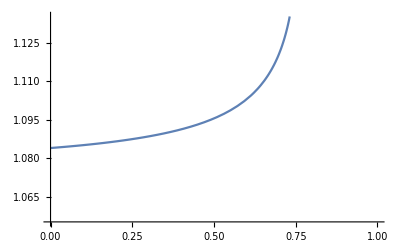

```mathematica
Plot[(zfp[x][M1,M2,M3,M4])/x,{x,0,1}]
```

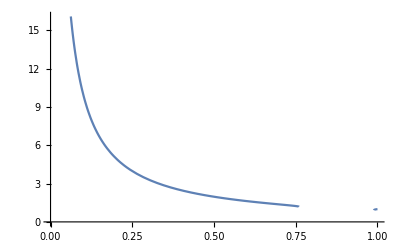

```mathematica
Plot[(zfn[x][M1,M2,M3,M4])/x,{x,0,1}]
```

```mathematica
Block[{z,ω},ParallelTable[z=zfn[0.5][M1,M2,M3,M4];{ω,(1+ℂ)If[ω>z,Print["error, ω overflow"],(1-z)/ω NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x]Kernel2PV[ϕ3,ϕ1][1-(1-x)(1-z)/ω,z,ω],{x,0,1}]]},{ω,0.1,0.99,0.01}]]
```

$Aborted

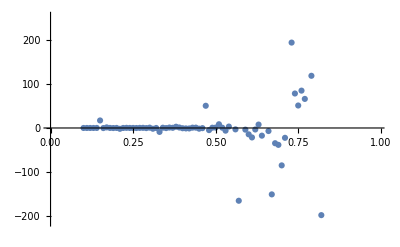

```mathematica
ListPlot[%35]
```

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4]},(1+ℂ)If[ω>z,-(1-ω)/z NIntegrate[ϕ2[(1-ω)/(1-z)x]ϕ4[x](ϕ1[y]ϕ3[z/ω y])/(y-(1-(1-x)(1-ω)/z))^2,{x,0,1},{y,0,1}],(1-z)/ω NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1}]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.832637,0.9942014165582343555860322936723605380393564701080322265625}. NIntegrate obtained 504.679 and 796.555 for the integral and error estimates.

17.4838

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x]Kernel2PV[ϕ3,ϕ1][1-(1-x)(1-z)/ω,z,ω],{x,0,1}]]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99994345953406560098856385027099591411570145282894372940063476562}. NIntegrate obtained -0.0272034-5.6697×10^-6 ⅈ and 4.21882×10^-8 for the integral and error estimates.

{8110.55,-0.0272034-5.6697×10^-6 ⅈ}

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1}]]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.982020378360022}. NIntegrate obtained -1620.58 and 1318.36 for the integral and error estimates.

{8.1629,-1620.58}

```mathematica
Block[{ω=0.3,z=zfp[0.3][M1,M2,M3,M4],λ=10^-6},Print[z,,(1-z)/(1-ω),,1-(1)(1-z)/ω];NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1-(1-x)(1-z)/ω-λ}]]//AbsoluteTiming
```

0.326574Null0.962037Null-1.24475

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0296336,0.000438096}. NIntegrate obtained 4.095389626254438579646656380215067350314273894559235719755627904×10^809-1.6353000275262249454721074561925999165969456694127187248117988389×10^797 ⅈ and 3.2988059203879788527592072086625962084585009375084219353750941509×10^809 for the integral and error estimates.

{24.9067,4.09538962625444×10^809}

```mathematica
Block[{ω=0.3,z=zfn[0.3][M1,M2,M3,M4],λ=10^-6},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1-(1-x)(1-z)/ω-λ},Method->"LocalAdaptive"]]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000110032,0.999999}. NIntegrate obtained 9.20435×10^-8 and 1.87054×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000113846,0.999999}. NIntegrate obtained 9.52781×10^-8 and 1.93627×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000117661,0.999999}. NIntegrate obtained 9.85131×10^-8 and 2.00201×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

$Aborted

```mathematica
Block[{ω=0.3,z=zfn[0.3][M1,M2,M3,M4],λ=10^-6},Print[(1-z)/(1-ω)];NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1}]]//AbsoluteTiming
```

0.0079919

{17.1299,1.84954-2.85023×10^-7 ⅈ}

```mathematica
Block[{ω=0.3,z=zfn[0.3][M1,M2,M3,M4],λ=10^-6},Print[(1-z)/(1-ω)];NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1},Method->"LocalAdaptive"]]//AbsoluteTiming
```

0.0079919

{214.729,1.84954}

```mathematica
Block[{ω=0.3,z=zfn[0.3][M1,M2,M3,M4],λ=10^-6},Print[(1-z)/(1-ω)];NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1},Method->"AdaptiveMonteCarlo",MaxPoints->10^6]]//AbsoluteTiming
```

0.0079919

{37.0917,1.8423}

```mathematica
Block[{ω=0.3,z=zfp[0.3][M1,M2,M3,M4],x=0.5,λ=10^-6},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1-(1-x)(1-z)/ω-λ}]+NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,1-(1-x)(1-z)/ω+λ,1}]-NIntegrate[2ϕ4[(1-z)/(1-ω)x]ϕ2[x]ϕ3[1-(1-x)(1-z)/ω] ϕ1[ω/z(1-(1-x)(1-z)/ω)]/λ,{x,0,1}]]//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.0296336,0.000438096}. NIntegrate obtained 4.095389626254438579646656380215067350314273894559235719755627904×10^809-1.6353000275262249454721074561925999165969456694127187248117988389×10^797 ⅈ and 3.2988059203879788527592072086625962084585009375084219353750941509×10^809 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5},ϕ4[(1-z)/(1-ω)x]ϕ2[x]Kernel2PV[ϕ3,ϕ1][1-(1-x)(1-z)/ω,z,ω]]//AbsoluteTiming
```

{13.1239,0.472489}

```mathematica
Block[{ω=0.58,z=zfp[0.58][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1},Method->"LocalAdaptive"]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.470294,0.670005}. NIntegrate obtained -0.000436214 and 0.00025577 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.470298,0.670005}. NIntegrate obtained 0.0101634 and 0.0654031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.470306,0.670009}. NIntegrate obtained -0.00284749 and 0.00466903 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

2.1801×10^11

```mathematica
Block[{ω=0.58,z=zfp[0.58][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1},Method->"MonteCarlo",MaxPoints->10^6]]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 9.15084×10^6 and 8.73333×10^6 for the integral and error estimates.

9.15084×10^6

```mathematica
Block[{ω=0.58,z=zfp[0.58][M1,M2,M3,M4]},NIntegrate[ϕ4[(1-z)/(1-ω)x]ϕ2[x](ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{x,0,1},{y,0,1},Method->"AdaptiveMonteCarlo",MaxPoints->10^6]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in y near {x,y} = {0.979151,0.987018}. NIntegrate obtained 9268.86 and 1286.71 for the integral and error estimates.

9268.86

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5},Kernel2PV[ϕ3,ϕ1][1-(1-x)(1-z)/ω,z,ω]]
```

-1.17556

```mathematica
Table[Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5,λ=10^-n},NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1-(1-x)(1-z)/ω-λ}]+NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,1-(1-x)(1-z)/ω+λ,1}]-2ϕ3[1-(1-x)(1-z)/ω] ϕ1[ω/z(1-(1-x)(1-z)/ω)]/λ],{n,1,10,0.5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.98267826838492863071855585276196969784275742076928850110562052578}. NIntegrate obtained 2.77626×10^7 and 144.75 for the integral and error estimates.

{-0.174722+2.86044×10^112 ⅈ,-0.483232+4.31552×10^41 ⅈ,-0.940662,-1.10151,-1.15215,-1.16818,-1.17324,-1.17484,-1.17535,-1.17551,-1.17556,-1.17557,-1.17548,-1.17588,-1.18637,-1.16914,-0.803903,8.03564,-24.1676}

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5,λ=10^-4},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1-(1-x)(1-z)/ω-λ}]]
```

0.979907

87.8743

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5,λ=10^-4},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,1-(1-x)(1-z)/ω+λ,1},MaxRecursion->20]]
```

0.979907

86.5386

0.908138

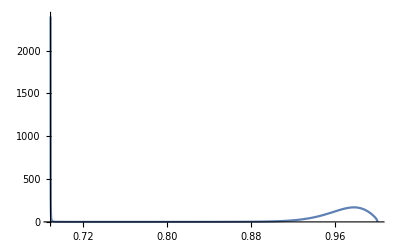

```mathematica
Block[{ω=0.58,z=zfp[0.58][M1,M2,M3,M4],x=0.5,λ=10^-4},Print[ω/z];Plot[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,1-(1-x)(1-z)/ω+λ,1},PlotRange->All]]
```

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1-(1-x)(1-z)/ω,1},Method->{"PrincipalValue"}]]
```

0.979907

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.35565×10^-59}. NIntegrate obtained 2.7003×10^244 and 2.66163×10^244 for the integral and error estimates.

2.7003×10^244

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5},Print[z];NIntegrate[(ϕ3[y]ϕ1[ω/z y])/(y-(1-(1-x)(1-z)/ω))^2,{y,0,1},Method->"LocalAdaptive"]]
```

0.979907

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.982678}. NIntegrate obtained 6609.92 and 0.0000112918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.982678}. NIntegrate obtained 8328.78 and 0.0000285474 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.982678}. NIntegrate obtained 8967.29 and 0.0000236435 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

1.00105×10^8

```mathematica
Block[{ω=0.58,z=zfn[0.58][M1,M2,M3,M4],x=0.5},1-(1-x)(1-z)/ω]
```

0.982678

```mathematica
Block[{ω=0.},1/(1-ω)NIntegrate[ϕ1[x]ϕ2[x/ω] ϕ3[p]/(p-(x-ω)/(1-ω))^2,{p,0,1},{x,0,ω},Method->"GlobalAdaptive"]-1/ω NIntegrate[ϕ1[x]ϕ3[(x-ω)/(1-ω)] ϕ2[p]/(p-x/ω)^2,{p,0,1},{x,ω,1},Method->"GlobalAdaptive"]]
```